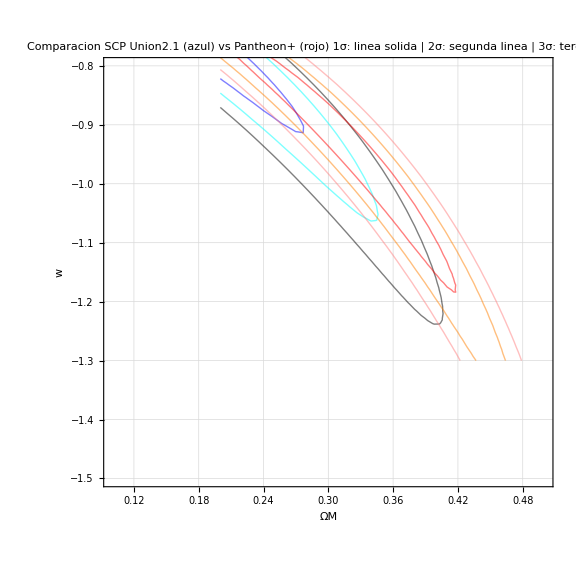

```mathematica
(*Leer datos SCP Union2.1*)datosU=Import["C:\\Users\\joses\\OneDrive\\Documents\\Mathematica\\chimin_2_1.dat","Table"];
puntosU=Transpose[{datosU[[All,1]],datosU[[All,2]],datosU[[All,3]]}];

(*Leer datos Pantheon+*)
datosP=Import["C:\\Users\\joses\\OneDrive\\Documents\\Mathematica\\chimin_P.dat","Table"];
puntosP=Transpose[{datosP[[All,1]],datosP[[All,2]],datosP[[All,3]]}];

(*Contour SCP Union2.1-tonos azules*)
contU=ListContourPlot[puntosU,Contours->{2.30,6.17,11.83},ContourStyle->{{Blue,Thick},{Cyan,Thick},{SkyBlue,Thick}},ContourShading->None,FrameLabel->{{"w",None},{"ΩM",None}},
PlotRange->{{0.1,0.5},{-1.5,-0.8}},
Frame->True,GridLines->Automatic,ImageSize->Large];

(*Contour Pantheon+-tonos rojos*)
contP=ListContourPlot[puntosP,Contours->{2.30,6.17,11.83},ContourStyle->{{Red,Thick},{Orange,Thick},{Pink,Thick}},ContourShading->None,

PlotRange->{{0.1,0.5},{-1.5,-0.8}},
Frame->True,GridLines->Automatic,ImageSize->Large];

(*Superponer ambos*)
Show[contU,contP,PlotLabel->"Comparacion SCP Union2.1 (azul) vs Pantheon+ (rojo)\n1σ: linea solida | 2σ: segunda linea | 3σ: tercera linea",PlotLegends->Placed[LineLegend[{Blue,Cyan,SkyBlue,Red,Orange,Pink},{"Union2.1 1σ","Union2.1 2σ","Union2.1 3σ","Pantheon+ 1σ","Pantheon+ 2σ","Pantheon+ 3σ"}],Right],ImageSize->Large]
```